SW: signs/symptoms/tests/...

Note to self

# Towards a Formalized Theory for the Foundations of Medicine

Need to do better than the gray cell background
Figure out the offset for the dotted border
Possibly label arrows   “insult”   /  “intervention”

SparseArray::list: List expected at position 1 in SparseArray[<||>].

Part::partd: Part specification SparseArray[<||>][NonzeroPositions]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification SparseArray[<||>][NonzeroPositions]⟦-1,1⟧ is longer than depth of object.

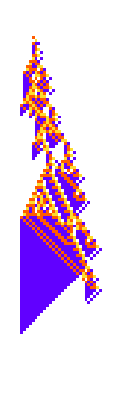
-Graphics-"healthy"-Graphics-"diseased"-Graphics-"with treatment"

```mathematica
Framed[Panel[Row[Labeled[Function[u,If[#2==="\"diseased\"",Show[u,Graphics[{EdgeForm[Directive[Hue[0.73, 0.91, 0.93, 0.41000000000000003],AbsoluteDashing[{3,1}]]],Opacity[0.4,Transparent],CAPolygon[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{110,{-6,218}},<||>]]}]],u]]@PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{110,{-110,110}},#1],"Trim"->{3,None},ImageSize->{Automatic,400},Background->White,FrameStyle->Directive[GrayLevel[0,.2]]],Text[Style[#2,Italic,GrayLevel[.4],FontSize->1.15 Inherited]]]&@@@{{<||>,"\"healthy\""},{<|{23,111}->2|>,"\"diseased\""},{<|{23,111}->2,{37,107}->3|>,"\"with treatment\""}},Spacer[20]],Background->Hue[0.73, 0.04, 0.98],FrameMargins->{60{1,1},10{1,1}}],FrameMargins->0,FrameStyle->Directive[Thick,Hue[0.73, 0.14, 0.93, 0.7000000000000001]]]
```

There’s unfortunate arrow pixelation here...

PM: From Jeremy below. Photoshopped labels. Fixed arrow pixelation

## A Theory of Medicine?

As it’s practiced today, medicine is almost always about particulars: “this has gone wrong; this is how to fix it”.  But might it also be possible to talk about medicine in a more general, more abstract way---and perhaps to create a framework in which one can study its essential features without engaging with all of its details?

My goal here is to take the first steps towards such a framework.  And in a sense my central result is that many broad phenomena in medicine seem at their core to be fundamentally computational---and to be captured by remarkably simple computational models that are readily amenable to study by computer experiment.

I should make it clear at the outset that I’m not trying to set up a specific model for any particular aspect or component of biological systems.  Rather, my goal is to “zoom out” and create what one can think of as a “metamodel” for studying and formalizing the abstract foundations of medicine.

What I’ll be doing builds on my recent work on using the computational paradigm to study the foundations of biological evolution.  And indeed in constructing idealized organisms we’ll be using the very same class of computational models.  But now, instead of considering idealized genetic mutations and asking what types of idealized organisms they produce, we’re going to be looking at specific evolved idealized organisms, and seeing what effect perturbations have on them.  Roughly, the idea is that an idealized organism will operate in its normal “healthy” way if there are no perturbations---but perturbations can “derail” the operation of the organism and introduce what we can think of as “disease”. And with this setup we can then think of the “fundamental problem of medicine” as being the identification of additional perturbations that can “treat the disease” and put the organism at least approximation back on its normal “healthy” track.

As we’ll see, most perturbations lead to lots of detailed changes in our idealized organisms, much as perturbations in biological organisms normally lead to vast numbers of effects, say at a molecular level.  But as in medicine, we can imagine that all we can observe (and perhaps all we care about) are certain coarse-grained “symptoms”.  And the fundamental problem of medicine is then to work out from these symptoms what “treatment” (if any) will end up being useful.  (By the way, when I say “symptoms” I mean the whole cluster of signs, symptoms, tests, etc. that one might in practice use, say for diagnosis.)

It’s worth emphasizing again that we’re not trying here to derive specific, actionable, medical conclusions.  Rather, my goal is to build a conceptual framework in which, for example, all sorts of widely observed phenomena in medicine that in the past have seemed at best vague and anecdotal can begin to be formalized and studied in a systematic way.  At some level, it’s a bit like what Darwinism brought to biological evolution.  But in modern times there’s a critical new element: the computational paradigm, which not only introduces all sorts of powerful new theoretical concepts, but also leads us to the practical new methodology of computer experimentation.  And indeed much of what follows will be based on the (often surprising) results of computer experiments that will allow us to progressively build our intuition---and structure our thinking---about fundamental phenomena in medicine.

## A Minimal Metamodel

How can we make a metamodel of medicine?  We need an idealization of biological organisms and their behavior and development.   We need an idealization of the concept of disease for such organisms.  And we need an idealization of the concept of treatment.

For our idealization of biological organisms we’ll use a class of simple computational systems called cellular automata (that I happen to have studied since the early 1980s).  Here’s a specific example:

Would be nice to use a less hacky RulePlot solution

For Developer

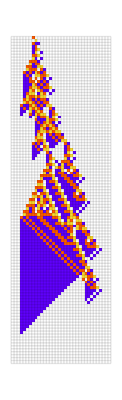
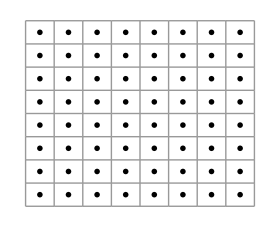

```mathematica
Row[{ArrayPlot[ArrayPad[CellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},110],{{0,0},{3,3}}],ColorRules->colorrules,ImageSize->{Automatic,520},Mesh->All,MeshStyle->Opacity[.1]],RulePlot[CellularAutomaton[{299459058088077823758143088095350287424,4,1}],ColorRules->colorrules][[1,1,All,All,1]]//Flatten//Partition[#,UpTo[8]]&//GraphicsGrid[#,Dividers->Directive[Thin,GrayLevel[.6]],ImageSize->280]&},Spacer[20]]
```

What’s going on here is that we’re progressively constructing the pattern on the left (representing the development and behavior of our organism) by repeatedly applying the rules on the right (representing the idealized genome---and other biochemical, etc. rules---of our organism).  Roughly we can think of the pattern on the left as corresponding to the “life history” of our organism---growing, developing and eventually dying as it goes down the page.  And even though there’s a rather organic look to the pattern, remember that the system we’ve set up isn’t intended to provide a model for any particular real-world biological system.  Rather, the goal is just for it to capture enough of the foundations of biology that it can serve as a successful metamodel to let us explore our questions about the foundations of medicine.

Looking at our model here in more detail, we see that it involves a grid of squares---or “cells” (computational, not biological)---each having one of 4 possible colors (white and three others).  We start from a single red “seed” cell on the top row of the grid, then compute the colors of cells on subsequent steps (i.e. on subsequent rows down the page) by successively applying the rules on the right.  The rules here are basically very simple.  But we can see that when we run them they lead to a fairly complicated pattern---which in this case happens to “die out” (i.e. all cells become white) after exactly 101 steps.

So what happens if we perturb this system?  On the left here we’re showing the system as above, without perturbation. But on the right we’re introducing a perturbation by changing the color of a particular cell (on step 16)---leading to a rather different (if qualitatively similar) pattern:

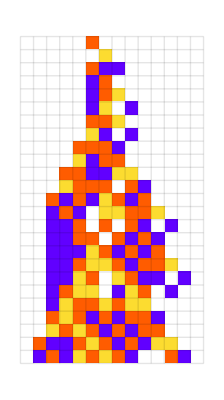
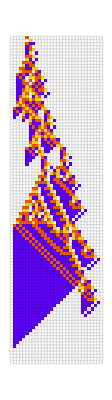
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[With[{ru={299459058088077823758143088095350287424,4,1},pt=<|{15,206}->0|>},{PlotCA[ru,"Steps"->24,ImageSize->{Automatic,200},Mesh->All,MeshStyle->Opacity[.1]],PlotCA[ru,"Steps"->105,ImageSize->{Automatic,450},Mesh->All,MeshStyle->Opacity[.1]],Spacer[20],PlotCA[PerturbedCellularAutomaton[ru,{{1},0},{24,{-200,200}},pt],Mesh->All,MeshStyle->Opacity[.1],ImageSize->{Automatic,200}],PlotCA[PerturbedCellularAutomaton[ru,{{1},0},{105,{-200,200}},pt],Mesh->All,MeshStyle->Opacity[.1],ImageSize->{Automatic,450}]}],Spacer[10],Alignment->Bottom]
```

Here are the results of some other perturbations to our system:

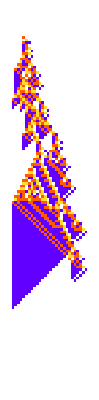
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
With[{ru={299459058088077823758143088095350287424,4,1}},Row[Insert[PlotCA[PerturbedCellularAutomaton[ru,{{1},0},{120,{-200,200}},#],ImageSize->{Automatic,330}]&/@{<||>,<|{16,203}->0|>,<|{37,208}->3|>,<|{15,206}->0|>,<|{28,209}->2|>,<|{23,202}->3|>,<|{32,207}->0|>},Spacer[10],2],Spacer[1]]]
```

Some perturbations (like the one in the second panel here) quickly disappear; in essence the system quickly “heals itself”.  But in most cases even single-cell perturbations like the ones here have a long-term effect.  Sometimes they can “increase the lifetime” of the organism; often they will decrease it.  And sometimes---like in the last case shown here---they will lead to essentially unbounded “tumor-like” growth.

In biological or medical terms, the perturbations we’re introducing are minimal idealizations of “things that can happen to an organism” in the course of its life.  Sometimes the perturbations will have little or no effect on the organism.  Or at least they won’t “really hurt it”---and the organism will “live out its natural life” (or even extend it a bit).  But in other cases, a perturbation can somehow “destabilize” the organism, in effect “making it develop a disease”, and often making it “die before its time”.

But now we can formulate what we can think of as the “fundamental problem of medicine”: given that perturbations have had a deleterious effect on an organism, can we find subsequent perturbations to apply that will serve as a “treatment” to overcome the deleterious effect?

The first panel here shows a particular perturbation that makes our idealized organism die after 47 steps.  And the subsequent panels show various “treatments” (i.e. additional perturbations) that serve at least to “keep the organism alive”:

Fix spacing etc.  [  cases in the middle are close together ; ends are further apart ]
Use (a)  etc.

For Developer

```mathematica
GraphicsRow[MapThread[Labeled[#1,Text[#2]]&,With[{u=PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {120, {-200, 200}}, #]]&/@{<|{23,202}->3|>,<|{23,202}->3,{57,214}->3|>,<|{23,202}->3,{44,209}->2|>,<|{23,202}->3,{34,208}->3|>,<|{23,202}->3,{26,204}->1|>,<|{23,202}->3,{31,202}->3|>,<|{23,202}->3,{35,207}->3|>,<|{23,202}->3,{52,211}->3|>, <||>}},{u,Take[Alphabet[],Length[u]]}]]]
```

-Graphics-

In the later panels here the “life history” of the organism gets closer to the “healthy” unperturbed form shown in the final panel.  And if our criterion is restoring overall lifetime, we can reasonably say that the “treatment has been successful”.  But it’s notable that the detailed “life history” (and perhaps “quality of life”) of the organism will essentially never be the same as before: as we’ll see in more detail later, it’s almost inevitably the case that there’ll be at least some (and often many) long-term effects of the perturbation+treatment.

So now that we’ve got an idealized model of the “problem of medicine”, what can we say about solving it?  Well, the main thing is that we can get a sense of why it’s fundamentally hard.  And beyond anything else, the central issue is a fundamentally computational one: the phenomenon of computational irreducibility.

Given any particular cellular automaton rule, with any particular initial condition, one can always explicitly run the rule, step by step, from that initial condition, to see what will happen.  But can one do better?  Experience with mathematical science might make one imagine that as soon as one knows the underlying rule for a system, one should in principle immediately be able to “solve the equations” and jump ahead to work out everything about what the system does, without explicitly tracing through all the steps.  But one of the central things I discovered in studying simple programs back in the early 1980s is that it’s common for such systems to show what I called computational irreducibility, which means that the only way to work out their detailed behavior is essentially just to run their rules step by step and see what happens.

So what about biology?  One might imagine that with its incremental optimization, biological evolution would produce systems that somehow avoid computational irreducibility, and (like simple machinery) have obvious easy-to-understand mechanisms by which they operate.  But in fact that’s not what biological evolution typically seems to produce.  And instead---as I’ve recently argued---what it seems to do is basically just to put together randomly found “lumps of irreducible computation” that happen to satisfy its fitness criterion.  And the result is that biological systems are full of computational irreducibility, and mostly aren’t straightforwardly “mechanically explainable”.  (The presence of computational irreducibility is presumably also why theoretical biology based on mathematical models has always been so challenging.)

But, OK, given all this computational irreducibility, how is that medicine is even possible?  How is it that we can know enough about what a biological system will do to be able to determine what treatment to use on it?  Well, computational irreducibility makes it hard.  But it’s a fundamental feature of computational irreducibility that within any computationally irreducible process there must always be pockets of computational reducibility.  And if we’re trying to achieve only some fairly coarse objective (like maximizing overall lifetime) it’s potentially possible to leverage some pocket of computational reducibility to do this.

(And indeed pockets of computational reducibility within computational irreducibility are what make many things possible---including having understandable laws of physics, doing higher mathematics, etc.)

## The Diversity and Classification of Disease

With our simple idealization of disease as the effect of perturbations on the life history of our idealized organism, we can start asking questions like “What is the distribution of all possible diseases?”

And to begin exploring this, here are the patterns generated with a random sample of the 4383 possible single-point perturbations to the idealized organism we’ve discussed above:

```mathematica
GraphicsGrid[Partition[Table[PlotCA[With[{ru={299459058088077823758143088095350287424,4,1}},SeedRandom[424324+i];PerturbedCellularAutomaton[ru,{{1},0},{150,{-8,36}},1]],"ArrowSize"->Small,"Trim"->{None,None},ImageSize->{Automatic,400}],{i,60}],15]]
```

-Graphics-

Clearly there’s a lot of variation in these life histories---in effect a lot of different symptomologies.  If we average them all together we lose the detail and we just get something close to the original:

```mathematica
pcas = With[{ru={299459058088077823758143088095350287424,4,1}},PerturbedCellularAutomaton[ru, {{1}, 0}, {150, {-10, 40}}, #, "ReturnPerturbations"->False]&/@ allperts[CellularAutomaton[ru, {{1}, 0}, {150, {-10, 40}}]]];
```

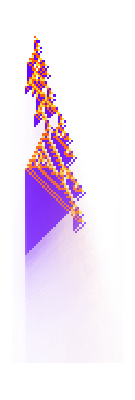

```mathematica
ArrayPlot[Map[Blend[Take[Last/@colorrules,4],BinCounts[#,{0,4,1}]]&,Transpose[pcas,{3,1,2}],{2}]]
```

But if we look at the distribution of lifetimes, we see that while it’s peaked at the original value, it nevertheless extends to both shorter and longer values:

Still to modernize ??

For Developer

```mathematica
lts = Block[{ru = {299459058088077823758143088095350287424,4,1}},
ca = getca[ru];
pcas = Flatten[PerturbAll[{ca, ru}, #]&/@ Flatten[bodyidxs[ca], 1], 1];
TestCALifeTime/@ pcas];
```

```mathematica
lts500=Block[{ru={299459058088077823758143088095350287424,4,1},ca,aps},ca=CellularAutomaton[ru,{{1},0},{500,All}];
aps=allperts[ca,ru[[2]]];
ParallelMap[TestCALifeTime[PerturbCA[{ca,ru},#]]&,aps]];
```

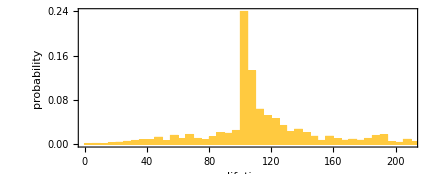

```mathematica
Histogram[lts500, 100, "Probability",Frame->True,AspectRatio->.4,FrameLabel->{"lifetime","probability"}]
```

Modernized hist

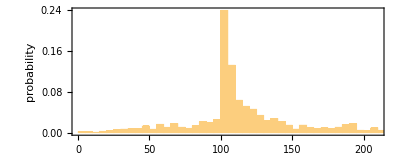

```mathematica
Module[
{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}},Histogram[TestCALifeTime[PerturbedCellularAutomaton[ru, init, txspec, #, "ReturnPerturbations"->False]]&/@ allperts[ru, init, txspec],  100, "Probability",Frame->True,AspectRatio->.4,FrameLabel->{"lifetime","probability"}]]
```

In medicine (or at least Western medicine) it’s been traditional to classify “things that can go wrong” in terms of discrete diseases.  And we can imagine also doing this in our simple model.  But it’s already clear from the array of pictures above that this is not going to be a straightforward story.  We’ve got a different detailed pattern for every different perturbation.  How should we group them together?

Well---much as in medicine---it depends on what we care about.  In medicine we would talk about symptoms, which in our idealized model we can basically identify with features of patterns.  And as an example, we might decide that the only features that matter are ones associated with the boundary shape of our pattern:

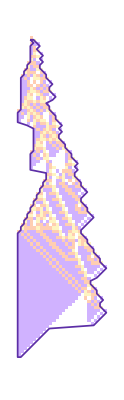
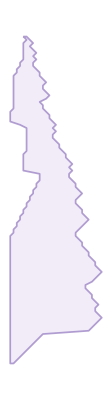
-Graphics--Graphics--Graphics-

```mathematica
Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={102,{-5,214}},aps,pca,ca},ca=CellularAutomaton[ru,init,txspec];
Row[{Show[
PlotCA[CellularAutomaton[ru,init,{102,{-10,30}}],"Trim"->{2,None},ColorRules->(#1->Lighter[#2,.7]&@@@colorrules),Frame->False],
Graphics[{EdgeForm[{Hue[0.73, 0.72, 0.65],AbsoluteDashing[{4,1}],AbsoluteThickness[1.25]}],FaceForm@Transparent,CAPolygon[ca]}],
ImageSize->{Automatic,250}
],Graphics[{GrayLevel[.3],AbsoluteThickness[1.25],Arrowheads[.6],Arrow[{{0,0},{1,0}}]},ImageSize->25],
Graphics[{EdgeForm[{Hue[0.73, 0.43, 0.72, 0.63],AbsoluteDashing[{4,1}],AbsoluteThickness[1.25]}],FaceForm@Hue[0.73, 0.14, 0.93, 0.36],CAPolygon[CellularAutomaton[ru,init,txspec]]},ImageSize->{Automatic,250}]}]]
```

So what happens to these boundary shapes with different perturbations?  Here are the most frequent shapes found (together with their probabilities):

```mathematica
silhouette2[list_,opts___]:=Graphics[{EdgeForm[{Hue[0.73, 0.43, 0.72, 0.63],AbsoluteDashing[{4,1}],AbsoluteThickness[1.25]}],Hue[0.73, 0.14, 0.93, 0.36],Polygon[Join[#1,Reverse[#2]]]&@@Transpose[MapIndexed[{#,-First[#2]}&,DeleteCases[list,{}],{2}]]},opts]
```

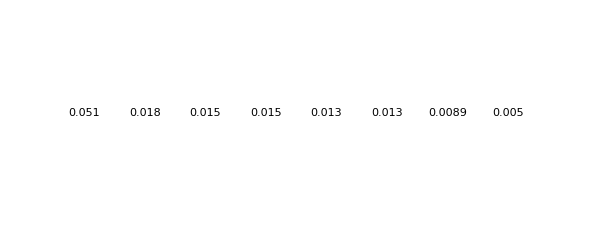

```mathematica
GraphicsRow[KeyValueMap[Labeled[silhouette2[#,Frame->True,FrameStyle->GrayLevel[0,.25],FrameTicks->None,ImageSize->{Automatic,200},PlotRange->{{190,230},{-120,0}}],Text[NumberForm[N[#2/Total[cts]],2]]]&,Take[ReverseSort[cts],8]]]
```

We might think of these as representing “common diseases” of our idealized organism.  But what if we look at all possible “diseases”---at least all the ones produced by single-cell perturbations?  Using boundary shape as our way to distinguish diseases we find that if we plot the frequency of diseases against their rank we get a rough power law distribution (and, yes, it’s not clear why it’s a power law):

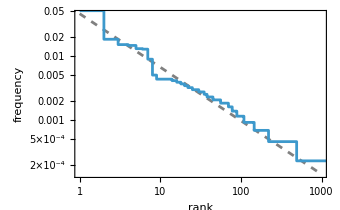

```mathematica
Show[Plot[0.04583459736390076/x^0.8374727002923698,{x,1,1000},ScalingFunctions->{"Log","Log"},PlotStyle->Directive[Dashed,Gray],Frame->True,FrameLabel->{"rank","frequency"}],ListStepPlot[Values[ReverseSort[cts]]/Total[Values[cts]],PlotRange->All,ScalingFunctions->{"Log","Log"},Frame->True,FrameLabel->{"rank","frequency"}]]
```

What are the “rare diseases” (i.e. ones with low frequency) like?  Their boundary shapes can be quite diverse:

Fix frame escapes
Use jeremy’s color

For Developer

Note: for some reason same seed is giving different shapes, does SW care?

```mathematica
ps = Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {130, {-110, 110}}},
SeedRandom[6353];Keys@*(RandomSample[Select[#,#==1&],60]&)@*ReverseSort@*Counts@*(CAPolygon[Take[PerturbedCellularAutomaton[ru, init, txspec, #, "ReturnPerturbations"->False], All, {90, 160}]]&/@ #&)@allperts[ru, init, txspec]];
```

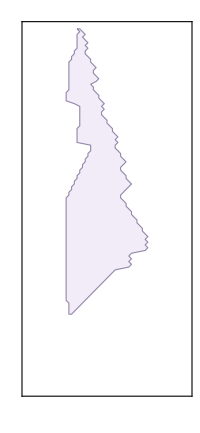
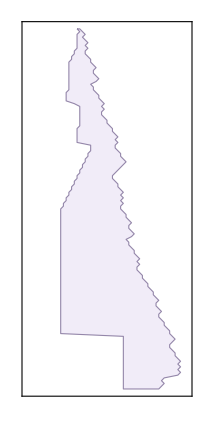
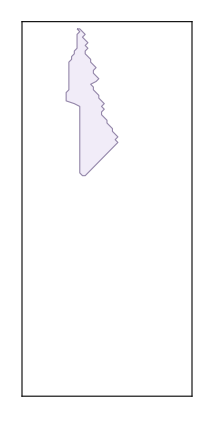
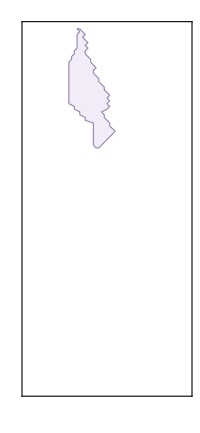
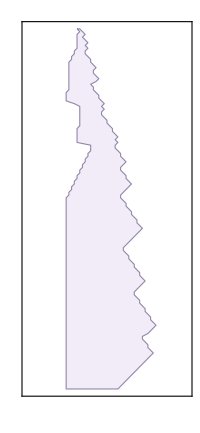
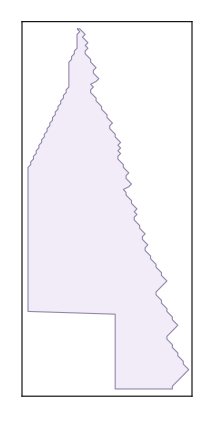
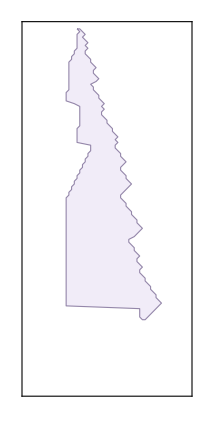
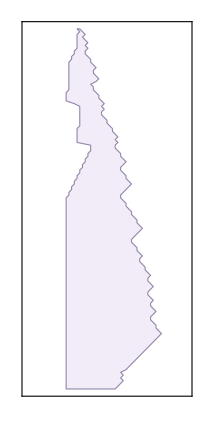

```mathematica
Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0}},GraphicsGrid@*(Partition[SeedRandom[6353];#, (*20*)20]&)@*
(Graphics[{EdgeForm[{Darker[Hue[0.73, 0.43, 0.72, 0.63]](*AbsoluteDashing[{4,1}],*)(*AbsoluteThickness[1.25]*)}],FaceForm@Hue[0.73, 0.14, 0.93, 0.36],#}, Frame->True,FrameTicks->None,PlotRange->{{3, 63},{0, 130}}]&/@#&)@ps]
```

But, OK, can we somehow quantify all these “diseases”?  For example, as a kind of “imitation medical test” we might look at how far to the left the boundary of each pattern ever goes.  With single-point perturbations, 84% of the time it’s the same as in the unperturbed case---but there’s a distribution of other, “less healthy” results (here plotted on a log scale)

Mark with dotted line the unperturbed case

For Developer

```mathematica
LaunchKernels["Local"];
```

```mathematica
pcas=Block[{ru={299459058088077823758143088095350287424,4,1},ca},ca=CellularAutomaton[ru,{{1},0},{400,{-200,200}}];
ParallelMap[PerturbedCellularAutomaton[ru,{{1},0},{400,{-200,200}},#,"ReturnPerturbations"->False]&,allperts[ca,4]]];
```

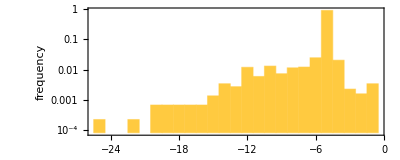

```mathematica
Histogram[-(201-Min[If[Length[#]==1,Infinity,Length[First[#]]]&[Split[#]]&/@#])&/@pcas,{1},{"Log","Probability"},Frame->True,AspectRatio->.4,FrameLabel->{"leftmost offset","frequency"},PlotRange->All]
```

with extreme examples being:

```mathematica
LaunchKernels["Local"];
```

```mathematica
pcas=Block[{ru={299459058088077823758143088095350287424,4,1},ca},ca=CellularAutomaton[ru,{{1},0},{400,{-200,200}}];
ParallelMap[PerturbedCellularAutomaton[ru,{{1},0},{400,{-200,200}},#,"ReturnPerturbations"->False]&,allperts[ca,4]]];
```

```mathematica
lefts=-(201-Min[If[Length[#]==1,Infinity,Length[First[#]]]&[Split[#]]&/@#])&/@pcas;
```

```mathematica
aps=Block[{ru={299459058088077823758143088095350287424,4,1},ca},ca=CellularAutomaton[ru,{{1},0},{400,{-200,200}}];allperts[ca,4]];
```

```mathematica
GraphicsRow[Labeled[Show[PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{200,{-200,200}},#],ImageSize->{Automatic,300}],Graphics[Style[Line[{{21,0},{21,200}}],Dotted]]],Text[#2]]&@@@({aps[[#]],lefts[[#]]}&/@{114,1417,1741,4302,1620,440,1618})]
```

-Graphics-

And, yes, we could diagnose any pattern that goes further to the left than the unperturbed one as a case of, say, “leftiness syndrome”.  And we might imagine that if we set up enough tests, we could begin to discriminate between many discrete “diseases”.  But somehow this seems quite ad hoc.

So can we perhaps be more systematic by using machine learning?  Let’s say we just look each whole pattern, then try to place it in an image feature space, say a 2D one.  Here’s an example of what we get:

Check.  Figure out about widths etc.  (probably OK)

Try making averages of the various clusters?

For Developer

```mathematica
FeatureSpacePlot[RandomSample[pcas,400],LabelingFunction->(PlotCA[#[[;;150]]]&),LabelingSize->50,Frame->True,FrameTicks->None,FrameStyle->Gray,RandomSeeding->64453]
```

-Graphics-

The details of this depend on the particulars of the machine learning method we’ve used (here the default FeatureSpacePlot method in Wolfram Language).  But it’s a fairly robust result that “visually different” patterns end up separated---so that in effect the machine learning is successfully automating some kind of “visual diagnosis”.  And there’s at least a little evidence that the machine learning will identify separated clusters of patterns that we can reasonably identify as “truly distinct diseases”---even as the more common situation is that between any two patterns, there are intermediate ones that aren’t neatly classified as one disease or the other.

Still, somewhat in the style of the human “International Classification of Diseases” (ICD), we can try arranging all our patterns in a hierarchy---though it’s basically inevitable that we’ll always be able to subdivide further, and there’ll never be a clear point at which we can say “we’ve classified all the diseases”.

*** Get examples

Make averages of subtrees

For Developer, note to self?

By the way, in addition to talking about possible diseases, we can talk about what counts as “healthy”.  We could say that our organism is only “healthy” if its pattern is exactly what it would be without any perturbation (“the natural state”).  But what probably better captures everyday medical thinking is to say that our organism should be considered “healthy” if it doesn’t have symptoms (or features) that we consider bad.  And in particular, at least “after the fact” we might say it must have been healthy if its lifetime turned out to be long.

It’s worth noting that even in our simple model, while there are many perturbations that reduce lifetime, there are also perturbations that increase lifetime.  In the course of biological evolution, genetic mutations of the overall underlying rules for our idealized organism might have managed to achieve a certain longevity.  But the point is that nothing says “longevity perturbations” applied “during the life of the organism” can’t get further---and indeed here are some examples where they do:

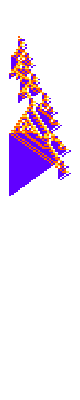
-Graphics-101-Graphics-122-Graphics-140-Graphics-148-Graphics-166-Graphics-157-Graphics-183-Graphics-201

```mathematica
Row[With[{u=PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{205,{-200,200}},#]},Labeled[PlotCA[u,ImageSize->{Automatic,250}],Text[Style[TestCALifeTime[u],Small]]]]&/@{<||>,<|{71,222}->3|>,<|{67,204}->1|>,<|{42,213}->2|>,<|{47,209}->1|>,<|{65,204}->0|>,<|{78,220}->2|>,<|{64,214}->3|>},Spacer[3]]
```

PM: from Brett and Jeremy. “The row spacing is sensitive to FontSize for some reason. The following reduces the space quite a bit...  Style[Row[ ...], FontSize -> .00001]”

```mathematica
Style[Row[With[{u=PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{205,{-200,200}},#]},Labeled[PlotCA[u,ImageSize->{Automatic,250}],Text[Style[TestCALifeTime[u],Small]]]]&/@{<||>,<|{71,222}->3|>,<|{67,204}->1|>,<|{42,213}->2|>,<|{47,209}->1|>,<|{65,204}->0|>,<|{78,220}->2|>,<|{64,214}->3|>},Spacer[3]],FontSize->0.00001]
```

-Graphics-101-Graphics-122-Graphics-140-Graphics-148-Graphics-166-Graphics-157-Graphics-183-Graphics-201

And, actually, in a feature that’s not (at least yet) reflected in human medicine, there are perturbations than can make the lifetime very significantly longer.  And for the particular idealized organized we’re studying here, the most extreme examples obtained with single-point perturbations are:

Halve spacing to make these fit on one line

```mathematica
Row[With[{u=PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{360,{-200,200}},#]},Labeled[PlotCA[u,ImageSize->{Automatic,300}],Text[Style[TestCALifeTime[First[u]],Small]]]]&/@aps[[Flatten[Reverse[PositionLargest[TestCALifeTime/@pcas,10]]]]],Spacer[.1]]
```

-Graphics-295-Graphics-304-Graphics-305-Graphics-308-Graphics-310-Graphics-320-Graphics-342-Graphics-349-Graphics-354-Graphics-356

PM: less spacing below

```mathematica
Style[Row[With[{u=PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{360,{-200,200}},#]},Labeled[PlotCA[u,ImageSize->{Automatic,300}],Text[Style[TestCALifeTime[First[u]],Small]]]]&/@aps[[Flatten[Reverse[PositionLargest[TestCALifeTime/@pcas,10]]]]],Spacer[.1]],FontSize->0.00001]
```

-Graphics-295-Graphics-304-Graphics-305-Graphics-305-Graphics-308-Graphics-310-Graphics-320-Graphics-342-Graphics-349-Graphics-354-Graphics-356

OK, but so what happens if we consider perturbations at multiple points?  There are immediately vastly more possibilities than with a single perturbations.  Here are some examples with two perturbations:

Cut off the edges rather than wrapping
? Arrow size

PM: from Jeremy: “arrow size isn’t bad... could be slightly small if there is control for that.”

Removed wrapping, shrunk arrows.

```mathematica
GraphicsGrid[Partition[Table[PlotCA[With[{ru={299459058088077823758143088095350287424,4,1}},SeedRandom[424324+i];PerturbedCellularAutomaton[ru,{{1},0},{150,{-50,50}},2]],"MaxWidth"->{40, 80},"Trim"->{None,None},"ArrowSize"->.2,ImageSize->{Automatic,400}],{i,30}],15]]
```

-Graphics-

Here with three perturbations:

```mathematica
GraphicsGrid[Partition[Table[PlotCA[With[{ru={299459058088077823758143088095350287424,4,1}},SeedRandom[425324+i];PerturbedCellularAutomaton[ru,{{1},0},{150,{-50,50}},3]],"MaxWidth"->{40, 80},"Trim"->{None,None},"ArrowSize"->.2,ImageSize->{Automatic,400}],{i,30}],15]]
```

-Graphics-

And here are examples of what happens when we try to apply five perturbations (though sometimes the organism is “already dead” before we can apply later perturbations):

```mathematica
GraphicsGrid[Partition[Table[PlotCA[With[{ru={299459058088077823758143088095350287424,4,1}},SeedRandom[425324+i];PerturbedCellularAutomaton[ru,{{1},0},{150,{-50,50}},5]],"MaxWidth"->{40, 80},"Trim"->{None,None},"ArrowSize"->.2,ImageSize->{Automatic,400}],{i,30}],15]]
```

-Graphics-

What happens to the overall distribution of lifetimes in these cases?  Already with two perturbations, the distribution gets much broader, and with three or more, the peak at the original lifetime has all but disappeared, while a new peak has appeared for organisms that in effect die almost immediately:

```mathematica
GraphicsGrid[Partition[Join[{Histogram[With[{ru={299459058088077823758143088095350287424,4,1}},TestCALifeTime[PerturbedCellularAutomaton[ru,{{1},0},{200,{-200,200}},#]]&/@allperts[CellularAutomaton[ru,{{1},0},{200,{-200,200}}]]],{2},"Probability",AspectRatio->.4,Frame->True,FrameTicks->{Automatic,None},Epilog->Text["1 perturbation",Scaled[{.85,.9}]]]},Table[Histogram[ParallelTable[With[{ru={299459058088077823758143088095350287424,4,1}},SeedRandom[424324+i];TestCALifeTime[PerturbedCellularAutomaton[ru,{{1},0},{200,{-200,200}},n]]],{i,10000}],{2},"Probability",AspectRatio->.4,Frame->True,FrameTicks->{Automatic,None},Epilog->Text[ToString[n]<>" perturbations",Scaled[{.85,.9}]]],{n,{2,3,5}}]],2]]
```

-Graphics-

In other words, the particular idealized organism that we’re studying is fairly robust against one perturbation, and perhaps even two, but if there are more perturbations it’s increasingly likely to succumb to “infant mortality”.   (And, yes, if one increases the number of perturbations the “life expectancy” progressively decreases.)

But what about the other way around?  With multiple perturbations, can the organism in effect “live forever”? Here are some examples where it’s still “going strong” after 300 steps:

```mathematica
GraphicsRow[(SeedRandom[2532735+#];PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{300,{-200,200}},2],"MaxWidth"->{110,270},"Trim"->{2,None}])&/@{21863,51317,45853,84319,61972,45314,71002,48527}]
```

-Graphics-

But after 500 steps most of these have died out:

```mathematica
GraphicsRow[(SeedRandom[2532735+#];PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{500,{-200,200}},2],"MaxWidth"->{110,290},"Trim"->{2,None}])&/@{21863,51317,45853,84319,61972,45314,71002,48527}]
```

-Graphics-

But as is typical in the computational universe (perhaps like in medicine) there are always surprises, courtesy of computational irreducibility.  Like the sudden appearance of the obviously periodic case (with period 25):

```mathematica
GraphicsRow[(SeedRandom[2532735+45853];PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{#,{-200,200}},2],"MaxWidth"->{110,290},"Trim"->{2,None}])&/@{100,200},Spacings->20]
```

-Graphics-

As well as the much more complicated cases (where in the final pictures the pattern has been “rectified”):

Fix silliness of last images

For Developer

```mathematica
vals=(SeedRandom[2532735+48527];First[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{4000,{-200,200}},2]]);
```

```mathematica
xperiod[seed_]:=Text["period "<>ToString[Last[Length/@FindTransientRepeat[(Total/@(SeedRandom[2532735+seed];(First@PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{3000,{-500,500}},2]))),2]]]]
```

```mathematica
GraphicsRow[{Labeled[GraphicsRow[(SeedRandom[2532735+45314];PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{#,{-500,500}},2],"MaxWidth"->{1,600},"Trim"->{2,None}])&/@{200,1000},ImageSize->{Automatic,240}],xperiod[45314]],Labeled[GraphicsRow[Append[(SeedRandom[2532735+48527];PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{#,{-500,500}},2],"MaxWidth"->{1,600},"Trim"->{2,None}])&/@{200,1000},GraphicsRow[PlotCA/@Partition[MapIndexed[RotateRight[#,Quotient[First[#2],2]-50]&,vals],2000],ImageSize->{Automatic,240}]],ImageSize->{Automatic,240}],xperiod[48527]]}]
```

-Graphics-

So, yes, in these cases the organism does in effect “live forever”.  But not in an “interesting” way.  And indeed such cases might remind us of tumor-like behavior in biological organisms.  But what about a case that not only lives forever, but also grows forever?  Well, needless to say, lurking out in the computational universe, one can find an example:

```mathematica
GraphicsRow[(SeedRandom[44359868];PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},#,2],"ArrowDirection"->"Right"])&/@{{100,{-200,200}},{1000,{-500,200}}}]
```

-Graphics-

The “incidence” of this behavior is about one in a million for 2 perturbations, and one in 300,000 for 3 perturbations.  And although there presumably is even more complicated behaviors out there to find, their incidence is below about one in 100 million.

Try to find case where we can’t tell if it will halt

For Developer

## Diagnosis & Prognosis

A fundamental objective in medicine is to predict from tests we do or symptoms we observe what will happen.  And, yes, we now know that computational irreducibility inevitably makes this in general hard.  But also know from experience that a certain amount of prediction is possible---which we can now interpret as successfully managing to tap into pockets of computational reducibility.

So as an example, let’s ask what the prognosis is for our idealized organism based on the width of its pattern we measure at a certain step.  So here, for example, is what happens to the original lifetime distribution (in green) if we consider only cases where the width of the measured pattern after 25 steps is less than its unperturbed (“healthy”) value (and where we’re dropping the 1% of cases when the organism was “already dead” before 25 steps):

```mathematica
pcas = With[{ru={299459058088077823758143088095350287424,4,1}},PerturbedCellularAutomaton[ru, {{1}, 0}, {400, {-30, 40}}, #]&/@ allperts[CellularAutomaton[ru, {{1}, 0}, {400, {-30, 40}}]]];
```

```mathematica
lts=TestCALifeTime/@pcas;
```

```mathematica
widths=If[Length[#]===0,0,Last[#]-First[#]+1]&[nonzeroRange[#]]&/@#&/@pcas[[All,1]];
```

```mathematica
Show[Histogram[Pick[lts,widths[[#,25]]<12&&widths[[#,25]]!=0&/@Range[Length[pcas]]],{3},"Probability",PlotRange->{{0,200},Automatic},Frame->True,FrameLabel->{"lifetime",None},AspectRatio->.4],Histogram[lts,{3},"Probability",ChartStyle->Opacity[.2,Green]]]
```

-Graphics-

Our “narrow” cases represent about 5% of the total.  Their median lifetime is 57, as compared with the overall median of 106.  But clearly the median alone does not tell the whole story.   And nor do the two survival curves:

Get the yellow right

```mathematica
Histogram[{lts,Pick[lts,widths[[#,25]]<12&&widths[[#,25]]!=0&/@Range[Length[pcas]]]},{1},"SF",Frame->True,FrameLabel->{"time","fraction surviving"},ChartStyle->{Opacity[.2,Green],Opacity[1,RGBColor[0.95, 0.627, 0.1425]]},AspectRatio->.4]
```

-Graphics-

PM: from Brett, the wrong color was being used. The yellow is RGBColor[1., 0.79375, 0.25]

```mathematica
pcas = With[{ru={299459058088077823758143088095350287424,4,1}},PerturbedCellularAutomaton[ru, {{1}, 0}, {400, {-30, 40}}, #]&/@ allperts[CellularAutomaton[ru, {{1}, 0}, {400, {-30, 40}}]]];
```

```mathematica
lts=TestCALifeTime/@pcas;
```

```mathematica
widths=If[Length[#]===0,0,Last[#]-First[#]+1]&[nonzeroRange[#]]&/@#&/@pcas[[All,1]];
```

```mathematica
Histogram[{lts,Pick[lts,widths[[#,25]]<12&&widths[[#,25]]!=0&/@Range[Length[pcas]]]},{1},"SF",Frame->True,FrameLabel->{"time","fraction surviving"},ChartStyle->{Opacity[.2,Green],Opacity[1,RGBColor[1., 0.79375, 0.25]]},AspectRatio->.4]
```

-Graphics-

And, for example, here are the actual widths as a function of time for all the narrow cases, compared to the sequence of widths for the unperturbed case:

```mathematica
pcas = With[{ru={299459058088077823758143088095350287424,4,1}},PerturbedCellularAutomaton[ru, {{1}, 0}, {400, {-30, 40}}, #]&/@ allperts[CellularAutomaton[ru, {{1}, 0}, {400, {-30, 40}}]]];
```

```mathematica
widths=If[Length[#]===0,0,Last[#]-First[#]+1]&[nonzeroRange[#]]&/@#&/@pcas[[All,1]];
```

```mathematica
width0=If[Length[#]===0,0,Last[#]-First[#]+1]&[nonzeroRange[#]]&/@PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {400, {-30, 40}}, <||>];
```

```mathematica
GraphicsRow[Show[ListStepPlot[Pick[widths,widths[[#,25]]<12&&widths[[#,25]]!=0&/@Range[Length[pcas]]],PlotRange->#,PlotStyle->RGBColor[0.95, 0.627, 0.1425],AspectRatio->.4,Frame->True,FrameLabel->{"step","width"}],ListStepPlot[width0,PlotStyle->RGBColor[0.24, 0.6, 0.8]]]&/@{{{0,50},{0,30}},{{0,240},Automatic}}]
```

-Graphics-

These pictures don’t make it look promising that one could predict lifetime from the single test of whether the pattern was narrow at step 25.  Like in analogous medical situations, one needs more data.  One approach in our case is to look at actual “narrow” patterns (up to step 25)---here sorted by ultimate lifetime---and then to try to identify useful predictive features (though to attempt any serious would require a lot more examples):

```mathematica
GraphicsGrid[Partition[PlotCA[Take[First@#,25],"PerturbationArrows"->False,"Trim"->{1,None},ImageSize->{Automatic,35}]&/@SortBy[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {400, {-30, 40}},#]&/@,TestCALifeTime],UpTo[30]]]
```

-Graphics-

But perhaps a simpler approach is not just to do a discrete “narrow or not” test, but rather to look at the actual width at step 25.  So here are the lifetimes as a function of width at step 25

```mathematica
BubbleChart[Select[KeyValueMap[Append[#1,#2]&,Counts[Transpose[{widths[[All, 25]], lts}]]],VectorQ[#,NumberQ]&],FrameLabel->{"width at step 25","lifetime"},AspectRatio->1/GoldenRatio]
```

-Graphics-

and here’s the distribution of outcomes, together with the median in each case:

Include x scale.  Lighten borders and perhaps histogram boxes

For Developer

```mathematica
Show[DistributionChart[Table[Lookup[KeySort[Map[Last,GroupBy[Transpose[{widths[[All,25]],lts}],First],{2}]],n,{}],{n,0,18}],ChartElementFunction->"HistogramDensity",FrameTicks->{Automatic,Automatic},FrameLabel->{"width at step 25","lifetime"}],ListStepPlot[KeySort[Median[Last/@#]&/@GroupBy[Transpose[{widths[[All,25]],lts}],First]],PlotRange->All]]
```

-Graphics-

PM: from Jeremy: “a bug in my code but the styles are correct (data doesn’t match draft)”

```mathematica
pcas = With[{ru={299459058088077823758143088095350287424,4,1}},PerturbedCellularAutomaton[ru, {{1}, 0}, {400, {-30, 40}}, #]&/@ allperts[CellularAutomaton[ru, {{1}, 0}, {400, {-30, 40}}]]];
```

```mathematica
widths=If[Length[#]===0,0,Last[#]-First[#]+1]&[nonzeroRange[#]]&/@#&/@pcas[[All,1]];
```

```mathematica
Show[DistributionChart[Table[Lookup[KeySort[Map[Last,GroupBy[Transpose[{widths[[All,25]],lts}],First],{2}]],n,{}],{n,0,18}],ChartElementFunction->"HistogramDensity",FrameTicks->{Automatic,Automatic},FrameLabel->{"width at step 25","lifetime"},ChartStyle->EdgeForm[Hue[0.11, 0.97, 0.77]]],ListStepPlot[KeySort[Median[Last/@#]&/@GroupBy[Transpose[{widths[[All,25]],lts}],First]],PlotRange->All,Filling->Bottom]]
```

-Graphics-

The predictive power of our width measurement is obviously quite weak (though there’s doubtless a way to “hack p values” to get at least something out).  And, unsurprisingly, machine learning doesn’t help.  Like here’s a machine learning prediction (based on decision tree methods) for lifetime as a function of width (that, yes, is very close to just being the median):

```mathematica
With[{p=Predict[Rule@@@Transpose[{widths[[All,25]],lts}]]},Plot[p[x],{x,0,18},PlotRange->All,Frame->True,FrameLabel->{"width at step 25","predicted lifetime"}]]
```

-Graphics-

Does it help if we use more history?  In other words, what happens if we make our prediction not just from at the width at a particular step, but from the history of all widths up to that point?  As one approach, we can make a collection of “training examples” of what lifetimes particular “width histories” (say up to step 25) lead to:

```mathematica
traindata=Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {25, {-110, 110}}, aps, pca, ca},((If[# == {}, 0,  #[[2]] - #[[1]] +1]&[nonzeroRange[#]]&/@ PerturbedCellularAutomaton[ru, init, txspec, #, "ReturnPerturbations"->False])->TestCALifeTime[PerturbedCellularAutomaton[ru, init, {400,{-110,110}}, #]])&/@ allperts[ru, init, txspec]];
```

```mathematica
Append[SeedRandom[2432424];ListStepPlot[#[[1]],PlotTheme->"Minimal",ImageSize->{80,Automatic},Frame->True,Filling->Axis,PlotRange->{0,20}]->Text[#[[2]]]&/@RandomSample[traindata,10],"…"]
```

{-Graphics-→37,-Graphics-→65,-Graphics-→33,-Graphics-→70,-Graphics-→104,-Graphics-→144,-Graphics-→78,-Graphics-→45,-Graphics-→57,-Graphics-→123,…}

There’s already something of an issue here, because a given width history---which, in a sense is a “coarse graining” of the detailed “microscopic” history---can lead to multiple different final lifetimes:

```mathematica
Append[KeyValueMap[ListStepPlot[#1,PlotTheme->"Minimal",ImageSize->{80,Automatic},Frame->True,Filling->Axis,PlotRange->{0,20}]->Text[Last/@#2]&,SeedRandom[2344242];RandomSample[Select[GroupBy[traindata,First],Length[Union[#]]>1&],10][[{1,2,6}]]],"…"]
```

{-Graphics-→{80,147,80,63,91},-Graphics-→{95,95,84},-Graphics-→{33,43},…}

FIND TEXT BEFORE CRASH!
Check claim about vertical line

For Developer

But we can still go ahead and try to use machine learning to predict lifetimes from width histories based on training on (say, half) of our training data---yielding less than impressive results (with the vertical line being associated with multiple lifetimes from a single width history in the training data):

PM: see text before crash below

But we can still go ahead and try to use some of our training examples to create a machine-learning predictor that we can use on other examples. The quality of the lifetime predictions we get this way are far from impressive; the strange vertical line is the result of the same width history leading to many different lifetimes:

debug weird error message
What’s with the seeding of the Predict ????

For Developer

```mathematica
Module[{ins=(SeedRandom[22354];RandomSample[Range[Length[traindata]],267])},outs=Complement[Range[Length[traindata]],ins];pd=Predict[traindata[[ins]],RandomSeeding->2524];ListPlot[{pd[First[#]],Last[#]}&/@traindata[[outs]],AspectRatio->.4,Frame->True,FrameLabel->{"predicted lifetime","actual lifetime"}]]
```

PredictorFunction::mlincfttp: Incompatible variable type (Boolean) and variable value (3).

PredictorFunction::mlincfttp: Incompatible variable type (Boolean) and variable value (3.).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

-Graphics-

PM: the code from the recording, see below. The results differ from the graph above.

```mathematica
traindata=Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={25,{-110,110}},aps,pca,ca},((If[#=={},0,#[[2]]-#[[1]]+1]&[nonzeroRange[#]]&/@PerturbedCellularAutomaton[ru,init,txspec,#,"ReturnPerturbations"->False])->TestCALifeTime[PerturbedCellularAutomaton[ru,init,{400,{-110,110}},#]])&/@allperts[ru,init,txspec]];
```

```mathematica
ListPlot[List@@@Module[{ins=(SeedRandom[24242];RandomSample[Range[Length[traindata]],300]),outs},pd=Predict[traindata[[ins]]];outs=Complement[Range[Length[traindata]],ins];pd[First[#]]->Last[#]&/@traindata[[outs]]],AspectRatio->.4,FrameLabel->{"prediction","actual"},Frame->True]
```

-Graphics-

So how can we do better?  Well, given the underlying setup for our system, if we could determine not just the width but the whole precise sequence of values for all cells, even just at step 25, then in principle we could use this as an “initial condition” and run the system forward to see what it does.  But regardless of it being “medically implausible” to do this, it isn’t much of a prediction anyway; it’s more just “watch and see what happens”.  And the point is that insofar as there’s computational irreducibility, one can’t expect---at least in full generality---to do much better.  (And, as we’ll argue later, there’s no reason to think that organisms produced by biological evolution will avoid computational irreducibility at this level.)

But still, within any computationally irreducible system, there are always pockets of computational reducibility.  So we can expect that there will be some predictions that can be made.  But the question is whether those predictions will be about things we care about (like lifetime) or even about things we can measure.  Or, in other words, will they predictions that speak to things like symptoms?

Our Physics Project, for example, involves all sorts of underlying processes that are computationally irreducible.  But the key point there is that what physical observers like us perceive are aggregate constructs (like overall features of space) that show significant computational reducibility.  And in a sense there’s an analogous issue here: there’s computational irreducibility underneath, but what do “medical observers” actually perceive, and are there computationally reducible features to that?  If we could find such things, then in a sense we’d have “general laws of medicine” much like we now have “general laws of physics”.

Perhaps add some examples based on more serious machine learning

For Developer

## The Problem of Finding Treatments

We’ve talked a bit about giving a prognosis for what will happen to an idealized organism that’s suffered a perturbation.  But what about trying to fix it?  What about trying to intervene with another “treatment” perturbation that can “heal” the system, and give it a life history that’s as close as possible to what it would have had without the original perturbation?

Here’s our original idealized organism, together with how it behaves when it “suffers” a perturbation that significantly reduces its lifetime:

```mathematica
Row[PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {105, {-110, 110}},#],"Trim"->{3,None},ImageSize->{Automatic,300}]&/@{<||>,<|{23,111}->2|>},Spacer[35]]
```

-Graphics--Graphics-

But what happens if we now try applying a second perturbation?  Here are a few random examples:

```mathematica
GraphicsRow[Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {102, {-110, 110}}, aps},
aps = Select[allperts[First[PerturbedCellularAutomaton[ru,init, txspec,<|{23,111}->2|>]]], Keys[#][[1, 1]]> 23&];PlotCA[PerturbedCellularAutomaton[ru,init, txspec,Join[<|{23,111}->2|>,#]]] &/@(SeedRandom[2842524];RandomSample[ aps,12])]]
```

-Graphics-

None of these examples convincingly “heal” the system.  But let’s say---as we can in our idealized model---that we just enumerate all possible second perturbations (here 1554 of them).  Then it turns out that a few of these perturbations do in fact successfully give us patterns that at least exactly reproduce the original lifetime:

```mathematica
healers = HealCA[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {110, {-110, 110}},<|{23,111}->2|>, All,#==101&];
```

```mathematica
GraphicsRow[PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {110, {-110, 110}},Join[<|{23,111}->2|>, #]]]&/@healers]
```

-Graphics-

Do these represent true examples of “healing”?  Well, it depends on what we mean.  Yes, they’ve managed to make the lifetime exactly what it would have been without the original “disease-inducing” perturbation.  But in essentially all cases we see that there are various kinds of “long-term side effects”---in the sense that the detailed patterns that are generated end up having obvious differences from the original unperturbed “healthy” form.

The one exception here is the very first case, in which the “disease was caught early enough” that the “treatment perturbation” manages to completely heal the effects of the “disease perturbation”:

Probably flip the plot to vertical

For Developer

```mathematica
Row[{GraphicsRow[PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {37, {-110, 110}},#],Mesh->True]&/@{<|{23,111}->2,{25,113}->3|>,<||>},Spacings->50],ListStepPlot[Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={110,{-110,110}}},Take[Normal[SparseArray[Normal[Counts[First/@SparseArray[CellularAutomaton[ru,init,txspec]-First[PerturbedCellularAutomaton[ru,init,txspec,<|{23,111}->2,{25,113}->3|>]]]["NonzeroPositions"]]],First[txspec]]],60]],AspectRatio->.3,Frame->True,FrameLabel->{"step","number of differences"},PlotRange->{-.1,3.5},FrameTicks->{{Range[0,3],None},{Automatic,None}}]}]
```

-Graphics--Graphics-

We’ve been talking here about intervening with “treatment perturbations” to “heal” our “disease perturbation”.  But actually it turns out that there are plenty of “disease perturbations” which automatically “heal themselves”, without any “treatment” intervention.  In fact, of all possible 4383 single perturbations, 380 essentially heal themselves.

In many cases, the “healing” happens very locally, after one or two steps:

Try a glow for the change pixels

For Developer

```mathematica
GraphicsGrid[{PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {20, {-110, 110}},#]]&/@{<||>,<|{15,109}->1|>,<|{16,113}->0|>,<|{14,108}->1|>,<|{15,114}->0|>},Prepend[Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={20,{-110,110}}},PlotDifferences[CellularAutomaton[ru,init,txspec ],First@PerturbedCellularAutomaton[ru,init,txspec,#]]]&/@{<|{15,109}->1|>,<|{16,113}->0|>,<|{14,108}->1|>,<|{15,114}->0|>},Graphics[]]}]
```

-Graphics-

PM: photoshopped example from Jeremy below:

Looks nice...

But there are also more complicated cases, where perturbations produce fairly large-scale changes in the pattern---that nevertheless “spontaneously heal themselves”:

Fix silly spacing

For Developer

```mathematica
GraphicsGrid[{PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {102, {-110, 110}},#]]&/@{<||>,<|{56,114}->1|>,<|{58,117}->0|>,<|{58,119}->3|>,<|{55,115}->0|>,<|{66,126}->0|>},Prepend[Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={102,{-110,110}}},PlotDifferences[CellularAutomaton[ru,init,txspec ],First@PerturbedCellularAutomaton[ru,init,txspec,#]]]&/@{<|{56,114}->1|>,<|{58,117}->0|>,<|{58,119}->3|>,<|{55,115}->0|>,<|{66,126}->0|>},Graphics[]]}]
```

-Graphics-

(Needless to say, in cases where a perturbation “spontaneously heals itself”, adding a “treatment perturbation” will almost always lead to a worse outcome.)

So how should we think about perturbations that spontaneously heal themselves?  They’re like seeds for diseases that never take hold, or like diseases that quickly burn themselves out.  But from a theoretical point of view we can think of them as being cases where the unperturbed life history of our idealized organism is acting as attractor, to which certain perturbed states inexorably converge---a bit like how friction can dissipate perturbations to patterns of motion in a mechanical system.

But let’s say we have a perturbation that doesn’t “spontaneously heal itself”.  Then to remediate it we have to do the “medical thing” and in our idealized model try to find a “treatment perturbation”.  So how might we systematically set about doing that?  Well, in general, computational irreducibility makes it difficult.  And as one indication of this, this shows what lifetime is achieved by making a “treatment perturbation” at each possible point in the pattern after the initial perturbation:

Non-hackily fix heights.  Put more space between the 2 left panels and 2 right ones

For Developer

```mathematica
GraphicsRow[Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={200,{-110,110}},aps,pca,ca,lt},ca=PerturbedCellularAutomaton[ru,init,txspec,{}];
{PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {105, {-110, 110}},<||>],"Trim"->{3,None},ImageSize->{Automatic,500},Mesh->True,MeshStyle->Opacity[.1]],PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {105, {-110, 110}},<|{23,111}->2|>],"Trim"->{3,None},ImageSize->{Automatic,500},Mesh->True,MeshStyle->Opacity[.1]],TherapySensitivityPlot[ru,init,txspec,<|{23,111}->2|>,"MaxLength"->105,Mesh->True,MeshStyle->Opacity[.1]],ArrayPlot[Table[Table[x,4],{x,1,101}],Mesh->{True,False},MeshStyle->Opacity[.1],ColorFunctionScaling->True,ColorFunction->(If[#<.225,LightGray,If[#==1,Darker[Red],Blend[Reverse@{Red,Orange,Lighter[Orange,.9],Yellow},#-.225]]]&)]}]]
```

-Graphics-

```mathematica
GraphicsRow[Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={200,{-110,110}},aps,pca,ca,lt},ca=PerturbedCellularAutomaton[ru,init,txspec,{}];
{PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {105, {-110, 110}},<||>],"Trim"->{3,None},ImageSize->{Automatic,500},Mesh->True,MeshStyle->Opacity[.1]],PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {105, {-110, 110}},<|{23,111}->2|>],"Trim"->{3,None},ImageSize->{Automatic,500},Mesh->True,MeshStyle->Opacity[.1]],TherapySensitivityPlot[ru, init, txspec,<|{23,111}->2|>, "MaxLength"->105, Mesh->True, MeshStyle->Opacity[.1], ImageSize->{Automatic, 500}],ArrayPlot[Table[Table[x,4],{x,1,101}], ColorFunctionScaling->True,MeshStyle->Opacity[0.1], ColorFunction->(If[#< .225, LightGray,If[#==1,Darker[Red],
Blend[Reverse@{Orange, Lighter[Orange, .2], Lighter[Orange, .4],  Yellow},#-.225]]]&), Mesh->{True, False} ,ImageSize->{Automatic, 500}]}]]
```

-Graphics-

We can think of this as providing a map of what the effects of different treatment perturbations will be.  Here are some other examples, for different initial perturbations (or, in effect, different “diseases”):

```mathematica
GraphicsRow[Append[Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},
ca = PerturbedCellularAutomaton[ru, init, txspec, {}];
TherapySensitivityPlot[ru, init, txspec,#,"MaxLength"->105]&/@ (allperts[First[ca]][[441;;450]] )], ArrayPlot[Table[Table[x,4],{x,1,101}], ColorFunctionScaling->True,MeshStyle->Opacity[0.1], ColorFunction->(If[#< .225, LightGray,If[#==1,Darker[Red],
Blend[Reverse@{Orange, Lighter[Orange, .2], Lighter[Orange, .4],  Yellow},#-.225]]]&), Mesh->{True, False} ,ImageSize->{Automatic, 500}]]]
```

-Graphics-

There’s some regularity here.  But the main observation is that different detailed choices of treatment perturbations will often have very different effects.  In other words, even “nearby treatments” will often lead to very different outcomes.  Given computational irreducibility, this isn’t surprising.  But in a sense it underscores the difficulty of finding and applying “treatments”.  By the way, cells indicated in dark red above are ones where treatment leads to a pattern that lives “excessively long”---or in effect shows tumor-like characteristics.   And the fact that these are scattered so seemingly randomly reflects the difficulty of predicting whether such effects will occur as a result of treatment.

In what we’ve done so far here, our “treatment” has always consisted of just a single additional perturbation.  But what applying more perturbations?  For example, let’s say we do a series of experiments where after our first “treatment perturbation” we progressively try other treatment perturbations.  If a given additional perturbation doesn’t get further from the desired lifetime, we keep it.  Otherwise we reject it, and try another perturbation.  Here’s an example of what happens if we do this:

Clean up variable scoping in code

For Developer

```mathematica
ttt=With[{i=5},With[{ip =<|{23,111}->2|>,
ica = PerturbedCellularAutomaton[ru, {{1}, 0}, {200, {-110, 110}}, ip],
ilt = Replace[TestCALifeTime[ica], -Infinity:> 401],
iaps = Select[allperts[First[ica], ru[[2]]], Keys[#][[1, 1]]>= Keys[ip][[-1, 1]]&]}, 
Module[{ru ={299459058088077823758143088095350287424,4,1}, ltgoal = TestLifetime[ru, 400], pca,llt},
SeedRandom[333557 + i];
Reap[Sow[{ip,ilt,ilt}];NestWhileList[
Function[{fitness, perts, aps},
pca = PerturbedCellularAutomaton[ru, {{1}, 0}, {400, {-110, 110}}, Join[perts, RandomChoice[aps]]];
llt=TestCALifeTime[First[pca]];plt = Replace[llt, -Infinity:> 401];Sow[{Last[pca],llt,If[Abs[plt - ltgoal] <= Abs[fitness-ltgoal],plt,fitness]}];
If[Abs[plt - ltgoal] <= Abs[fitness-ltgoal], {plt, Join[perts, Last[pca]],Select[allperts[First[pca], ru[[2]]], Keys[#][[1, 1]]>= Keys[Last[pca]][[-1, 1]]&]}, {fitness, perts, aps}]
]@@#&, {ilt,ip, iaps},Last[#]=!={}&,1,14]]]]];
```

```mathematica
GraphicsRow[Labeled[PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {105, {-110, 110}}, #[[1]]],FrameStyle->If[#[[2]]==#[[3]],Directive[Black,Thick],Automatic],ImageSize->{Automatic,180}],Text[Style[#[[2]],Small]]]&/@ttt[[2,1]]]
```

-Graphics-

The highlighted panels represent perturbations that were kept.  An here’s how the overall lifetime “converges” in successive iterations of our experiment:

```mathematica
With[{q=ttt[[-1,1]]},Show[ListStepPlot[q[[All,3]]],ListPlot[q[[All,2]],PlotStyle->Red,Filling->Bottom],PlotRange->{{.8,15.5},{50,120}},Frame->True,FrameLabel->{"iteration","lifetime"},AspectRatio->.4,Axes->None]]
```

-Graphics-

In what we just did, we allowed additional treatment perturbations to be added at any subsequent step.  But what if we require that treatment perturbations always be added on successive steps---starting right after the “disease perturbation” occurred?   Here’s an example of what happens in this case:

Put in highlights for improvement cases
Remove the hack for the initial state

For Developer

```mathematica
txiseq[i_,cut_,max_]:=Module[{plt,ilt,iaps,ru={299459058088077823758143088095350287424,4,1},ip=<|{23,111}->2|>,ica},ica = PerturbedCellularAutomaton[ru, {{1}, 0}, {200, {-110, 110}}, ip];ilt = Replace[TestCALifeTime[ica], -Infinity:> 401];
iaps = Select[allperts[First[ica], ru[[2]]], Keys[#][[1,1]]-Keys[ip][[-1,1]]==cut&];With[{ttt=
Module[{ ltgoal = TestLifetime[ru, 400], pca,llt},
SeedRandom[333557 + i];
Reap[Sow[{ip}];NestWhileList[
Function[{fitness, perts, aps},
pca = PerturbedCellularAutomaton[ru, {{1}, 0}, {400, {-110, 110}}, Join[perts, RandomChoice[aps]]];
llt=TestCALifeTime[First[pca]];plt = Replace[llt, -Infinity:> 401];Sow[{Last[pca],llt,If[Abs[plt - ltgoal] <= Abs[fitness-ltgoal],plt,fitness]}];
If[Abs[plt - ltgoal] <= Abs[fitness-ltgoal], {plt, Join[perts, Last[pca]],Select[allperts[First[pca], ru[[2]]],Keys[#][[1,1]]-Keys[Last[pca]][[-1,1]]==cut&]}, {fitness, perts, aps}]
]@@#&, {ilt,ip, iaps},Last[#]=!={}&,1,max]]]},With[{u=Cases[ttt[[2,1]],{_,x_,x_}]},First/@Split[Take[u,If[!IntegerQ[#],Length[u],First@#]&[FirstPosition[Last/@u,101]]]]]]]
```

```mathematica
Labeled[PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {105, {-110, 110}}, #[[1]]],ImageSize->{Automatic,180}],Text[Style[#[[2]],Small]]]&/@Prepend[txiseq[10,1,100],{<|{23,111}->2|>,66,66}]
```

{-Graphics-66,-Graphics-111,-Graphics-105,-Graphics-105,-Graphics-102,-Graphics-101,-Graphics-101,-Graphics-101}

And here’s what we see zooming at the beginning:

```mathematica
Row[Insert[Table[PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {35, {-110, 110}},First[txiseq[10,1,100][[i]]]],Mesh->True,ImageSize->{Automatic,200}],{i,{1,2,3,-1}}],"…",4],Spacer[10]]
```

-Graphics--Graphics--Graphics-…-Graphics-

In a sense this corresponds to “doing aggressive treatment” as soon as the initial “disease perturbation” has occurred.  And a notable feature of the particular example here is that when our succession of treatment perturbations have succeeded in “restoring the lifetime” (which happens fairly quickly), the life history they produce is similar (though not identical) to the original unperturbed case.

That definitely doesn’t always happen, as this example illustrates---but it’s fairly common:

```mathematica
Labeled[PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {105, {-110, 110}}, #[[1]]],ImageSize->{Automatic,180}],Text[Style[#[[2]],Small]]]&/@txiseq[9,1,100]
```

{-Graphics-66,-Graphics-111,-Graphics-105,-Graphics-100,-Graphics-100,-Graphics-100,-Graphics-102,-Graphics-101}

It’s worth pointing out that if we allowed ourselves to do many single perturbations at the same time (i.e. on the same row of the pattern) we could effectively just “define new initial conditions” for the pattern, and, for example, perfectly reproduce the original unperturbed pattern after this “reset”.  And in general we can imagine in effect “hot-wiring” the organism by applying large numbers of treatment perturbations that just repeatedly direct it back to its unperturbed form.

But such extensive and detailed “intervention”---that in effect replaces the whole state of the organism---seems far from what might be practical in actual (current) medicine.  And indeed in actual (current) medicine one is normally operating in a situation where one does not have anything close to perfect “cell by cell” information on the state of an organism---and instead one has to figure out things like what treatment to give based on much coarser “symptom-level” information.

So what can one do in the presence that kind of limitation?  As one example, let’s consider trying to predict what treatment perturbation will be best based purely on the kind of pattern-width information we discussed above.  Specifically, let’s say that we have the history of the overall width of a certain pattern up to a particular point, then from this we want to predict what treatment perturbation will lead to the best lifetime outcome for the system.  There are a variety of ways we could approach this, but one is to make predictions of where to apply a treatment perturbation using machine learning trained on examples of optimal such perturbations.

This is analogous to what we did in the previous section in applying machine learning to predict lifetime from width history.  But now we want to predict from the width history where to apply a treatment perturbation.  To generate our training data we can search for treatment perturbations that lead to the unperturbed lifetime when starting from life histories with a given width history.  Now we can use machine learning to create a predictor that tries to tell us from a width history where to apply a treatment perturbation.  And, once again, the results aren’t particularly impressive:

more to do

For Developer

```mathematica
awh = Module[{ru = {299459058088077823758143088095350287424,4,1},init = {{1}, 0},txspec =  {200, {-110, 110}}, aps, pca, ca},(If[# == {}, 0,  #[[2]] - #[[1]] +1]&[nonzeroRange[#]]&/@ PerturbedCellularAutomaton[ru, init, txspec, #, "ReturnPerturbations"->False]&/@ allperts[ru, init, txspec])];
```

[[[ predict vs actual ]]]

At step 50, you’re trying to predict where to treat....

## The Effect of Genetic Diversity

One critical feature of actual medicine is that [[[ people aren’t all the same ... notably they have different genetics ....  ]]  [[ some of our “genetic elements  are noncoding ... but when there’s a perturbation, they get sampled....

```mathematica
plotmaskedrule[{299459058088077823758143088095350287424,4,1}]
```

-Graphics-

```mathematica
GraphicsGrid[MapAt[Show[#,Background->Gray]&,RulePlot[CellularAutomaton[{299459058088077823758143088095350287424,4,1}],ColorRules->colorrules][[1,1,All,All,1]]//Flatten,{{1},{2},{13}}]//Partition[#,UpTo[16]]&,Dividers->Directive[Thin,GrayLevel[.6]],ImageSize->280]
```

-Graphics-

There now 64 variants that correspond to different choices of those rule elements...

e.g. show a few different cases of those rules ......

```mathematica
quickneutral[{299459058088077823758143088095350287424,4,1}]//Length
```

64

Without perturbation they all behave the same...

[[ Show the original

```mathematica
KeyValueMap[Labeled[#1,Text[#2]]&,ReverseSort[Counts[PlotCA[PerturbedCellularAutomaton[#,{{1},0},{102,{-110,110}},<|{23,111}->2|>],ImageSize->{Automatic,150}]&/@quickneutral[{299459058088077823758143088095350287424,4,1}]]]]
```

{-Graphics-16,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1}

```mathematica
KeyValueMap[Labeled[#1,Text[#2]]&,ReverseSort[Counts[PlotCA[PerturbedCellularAutomaton[#,{{1},0},{300,{-110,110}},<|{23,111}->2|>],ImageSize->{Automatic,150}]&/@quickneutral[{299459058088077823758143088095350287424,4,1}]]]]
```

{-Graphics-16,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1}

```mathematica
KeyValueMap[Labeled[#1,Text[#2]]&,ReverseSort[Counts[PlotCA[PerturbedCellularAutomaton[#,{{1},0},{102,{-200,200}},<|{10,203}->0|>],ImageSize->{Automatic,150}]&/@quickneutral[{299459058088077823758143088095350287424,4,1}]]]]
```

{-Graphics-16,-Graphics-16,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1}

Overall effect on lifetime:

```mathematica
ParallelMap[Histogram[Module[{ru = #,ca,pcas},
ca = getca[ru];
pcas = Flatten[PerturbAll[{ca, ru}, #]&/@ Flatten[bodyidxs[ca], 1], 1];
TestCALifeTime/@ pcas]/.-Infinity->250, 50, PlotRange->All]&,quickneutral[{299459058088077823758143088095350287424,4,1}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[[[ same analyses; different genomes ]]]

[[ Therapy that works on one genome doesn’t necessarily work on others .... show all 64 cases ]]

## Biological Evolution and Our Model Organism

[[ Could be whole organism, or could be e.g. an organ ]]

```mathematica
rh = Reap[mh = Module[{ru,ca,lt,lts, pcas,fitness},SeedRandom[7899623];
NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
ca=CellularAutomaton[ru,{{1},0},{200,All}];
lt=TestCALifeTime[ca];
If[lt==-Infinity,Sow[{ru, <||>,{lt}}];#,
pcas=Table[PerturbedCellularAutomaton[ru,{{1},0},{200,{-200,200}},1],Ceiling[lt/10]];
fitness=Min[lts = Join[{lt},TestCALifeTime/@(First/@pcas)]];
Sow[{ru, Last/@pcas,lts}];
If[fitness>=Last[#],{ru,fitness},#]]]&,{{0,4,1},0},2000]]][[2, 1]];
```

```mathematica
Labeled[PlotCA[First[#],"Trim"->{1,5},ImageSize->{Automatic,25 Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@(First/@SplitBy[mh,Last])
```

{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-7,-Graphics-9,-Graphics-12,-Graphics-14,-Graphics-15,-Graphics-37,-Graphics-38,-Graphics-40,-Graphics-49,-Graphics-60,-Graphics-68,-Graphics-84,-Graphics-101}

```mathematica
Show[ListStepPlot[mh[[All, 2]]], ListPlot[Min/@rh[[All, 3]], PlotHighlighting->None, PlotStyle->Red],Frame->True,AspectRatio->1/3]
```

-Graphics-

Use gray lines (maybe) for the perturbed stuff

For Developer

```mathematica
Show[ListStepPlot[mh[[All, 2]]], ListPlot[{Style[Catenate[MapIndexed[{First[#2],#1}&,rh[[All, 3]],{2}]],Opacity[.2,Gray]], Style[MapIndexed[{First[#2],#}&,Min/@rh[[All, 3]]],Red]},PlotHighlighting->None],Frame->True,AspectRatio->1/3]
```

-Graphics-

points seem to be off by 1

For Developer

```mathematica
Show[ListStepPlot[mh[[All, 2]]], ListPlot[{Style[Catenate[MapIndexed[{First[#2],#1}&,rh[[All, 3]],{2}]],Opacity[.5,Gray],PointSize[Large]], Style[MapIndexed[{First[#2],#}&,Min/@rh[[All, 3]]],PointSize[Large],Red]},PlotHighlighting->None],Frame->True,AspectRatio->1/3,PlotRange->{{0,50},{0,10}}]
```

-Graphics-

```mathematica
Show[ListStepPlot[mh[[All, 2]]], ListPlot[{Style[Catenate[MapIndexed[{First[#2],#1}&,rh[[All, 3]],{2}]],Opacity[.5,Gray],PointSize[Large]], Style[MapIndexed[{First[#2],#}&,Min/@rh[[All, 3]]],PointSize[Large],Red]},PlotHighlighting->None],Frame->True,AspectRatio->1/3,PlotRange->{{0,200},{0,12}}]
```

-Graphics-

```mathematica
With[{wins=Echo@ResourceFunction["ProgressiveMaxPositions"][DeleteCases[Min/@rh[[All, 3]],-Infinity]]},Show[ListStepPlot[mh[[All, 2]]], ListPlot[{Style[Catenate[MapIndexed[If[MemberQ[wins,#],Callout[{First[#2],#1},Graphics[Disk[],ImageSize->50]],{First[#2],#1}]&,rh[[All, 3]],{2}]],Opacity[.2,Gray]], Style[MapIndexed[{First[#2],#}&,Min/@rh[[All, 3]]],Red]},PlotHighlighting->None],Frame->True,AspectRatio->1/3]]
```

{1,6,9,22,75,78,137,183,189,190,250,251,260,267,268,273,300,530,881}

```mathematica
Show[ListStepPlot[mh[[All, 2]]], ListPlot[Min/@rh[[All, 3]], PlotHighlighting->None, PlotStyle->Red]]
```

```mathematica
With[{seq=ResourceFunction["ProgressiveMaxPositions"][
(Last/@mh)/.{-Infinity->0}]},Show[
ListStepPlot[Last/@mh,PlotRange->{0,125},
Frame->True,AspectRatio->1/3],
ListPlot[MapIndexed[If[MemberQ[Last@rh,First[#2]],
Callout[Last[#],Pane@ArrayPlot[
ArrayPad[#,1]&/@CellularAutomaton[
{#[[1]],3,1},{{1},0},1+Last[#]],
ColorRules->colorrules,
ImageSize->{Automatic, 10Sqrt[1+Last[#]]}],If[First[#2]!=Last[Last@rh],Above,Before],
LabelVisibility->All
],
mh[[All,2]][[First[#2]]]/.-Infinity->None
]&,mh],PlotStyle->Red,
LabelingSize->Full,
Frame->True,AspectRatio->1/3
]
]]
```

-Graphics-

Picture with  ... nn ...  between breakthroughs

** find the random seed etc. to generate this!
-11.nb

For Developer

```mathematica
First/@SplitBy[%,Last]
```

{{{0,4,1},0},{{633825300114114700748351602688,4,1},1},{{81763463720033458689778626068480,4,1},2},{{81763463720033458694315185274880,4,1},3},{{81931838076027891908402867077120,4,1},4},{{25967407559121214387661469853159531584,4,1},5},{{25967732077674872814392756608807478336,4,1},6},{{27320406588562325247900243404649442368,4,1},7},{{107074019143647262706119627567490706496,4,1},9},{{128341667036591835415448371735208438848,4,1},12},{{128341667026688315101165329536015445056,4,1},14},{{44247419788783520337962930866412350528,4,1},15},{{44247419788783520337962930866680785984,4,1},37},{{44247257529506691124599539288670497856,4,1},38},{{44247262600109092037517145275483319360,4,1},40},{{44247262614964372508941708574272810048,4,1},49},{{44247282897373976160612132521524096064,4,1},60},{{214388466357843207892299436237408201792,4,1},68},{{214388466357843207892299436237408234560,4,1},84},{{299459058088077823758143088095350287424,4,1},101}}

```mathematica
Labeled[PlotCA[First[#],"Trim"->{1,5},ImageSize->{Automatic,100}],Text[Style[Last[#],Small]]]&/@
```

{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-7,-Graphics-9,-Graphics-12,-Graphics-14,-Graphics-15,-Graphics-37,-Graphics-38,-Graphics-40,-Graphics-49,-Graphics-60,-Graphics-68,-Graphics-84,-Graphics-101}

instead of the plain loss curve, show the loss curve with all lifetimes at a given step
[ previously every genome had a single lifetime; now we have several lifetimes because of perturbations ]
( instead of showing individual red dots, join them vertically with a lighter line )

Like this:     [ expect to show a section in more detail ]

For Developer

[[ Show robustness to perturbations ]]

Show also non-robust longest living rules for this k=4 case  [ they will be much longer ]

For Developer

```mathematica
cands =DeleteDuplicates@ ;
```

```mathematica
PlotCA[CellularAutomaton[#,{{1},0},150]]&/@cands
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Show lifetime distributions for allperts

For Developer

## The Big Picture

[[ other applications ]].   [ Large systems ...  / computer security ]